## Kamen setup

```mathematica
kamen[x_]:=0.96-0.25(x-0.5)^2
FindRoot[kamen[x],{x,-2}]
```

{x→-1.45959}

```mathematica
kamenPlot=RegionPlot[y<0.96-0.25(x-0.5)^2,{x,-1.4595917942265424,2.4595917942265424},{y,0.5,1},PlotStyle->{Opacity[1],Texture[-Graphics-]},BoundaryStyle->Gray,TextureCoordinateFunction->({#1,#2}&)]
```

-Graphics-

#### String setup

```mathematica
k=1;
g=-1;
boundaryHeightLeft=1;
boundaryHeightRight=1;
boundaryLeft =0;
boundaryRight=1;
nXPoints=100;(* Tu klameme, nepocitame totiz bod v "boudaryLeft". Takze oficialne este je o jeden bod naviac. *)

(* Finite difference method - rozdelime x-ovu os na bodiky, v tychto bodoch pocitame "y" *)
dx=(boundaryRight-boundaryLeft)/nXPoints;
xPoints = Table[boundaryLeft+dx*i,{i,0,nXPoints}];

(*Toto navadza na sustavu rovnic -> matica*y=hodnoty, kde pozname maticu a hodnoty: (vid text)*)
matica = 1/dx^2* Table[If[i==j,2, If[Abs[i-j]==1,-1,0]],{i,0,nXPoints},{j,0,nXPoints}];
hodnoty = Table[-1+If[i==0 || i==nXPoints,1/dx^2,0],{i,0,nXPoints}];

(* Sustavu treba vyriesit. Kedze je to ilustracne, tak pouzivam LinearSolve, ale inak by sme to mali robit prave asi tym Newtonom, alebo ako. *)
ypsilony = LinearSolve[matica,hodnoty];
```

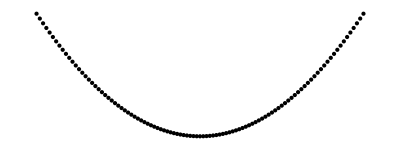

```mathematica
(* Transpose[{xPoints,ypsilony}]; *)
(* Previsnute body bez väzieb. *)
body = Graphics[Point[Transpose[{xPoints,ypsilony}]]]
```

## Praca s kamenom a String-om

```mathematica
ycords=Table[Subscript[y,i],{i,1,nXPoints-1}];
lambdas = Table[Subscript[λ,i],{i,1,nXPoints-1}];
ρ=10;
functions2[list_]:=Table[(-list[[i-1]]+2*list[[i]]-list[[i+1]])/dx^2+ 1+Piecewise[{{list[[nXPoints-1+i]]+ρ*(list[[i]]-kamen[xPoints[[i+1]]]),list[[nXPoints-1+i]]+ρ*(list[[i]]-kamen[xPoints[[i+1]]])<=0},{0,list[[nXPoints-1+i]]+ρ*(list[[i]]-kamen[xPoints[[i+1]]])>0}}],{i,2,nXPoints-2}];
functions4[list_]:=Table[Piecewise[{{(list[[i]]-kamen[xPoints[[i+1]]]),list[[nXPoints-1+i]]+ρ*(list[[i]]-kamen[xPoints[[i+1]]])<=0},{-list[[nXPoints-1+i]]/ρ,list[[nXPoints-1+i]]+ρ*(list[[i]]-kamen[xPoints[[i+1]]])>0}}],{i,1,nXPoints-1}];
functions1[list_]:={(-boundaryHeightLeft+2*list[[1]]-list[[2]])/dx^2+ 1+Piecewise[{{list[[nXPoints]]+ρ*(list[[1]]-kamen[xPoints[[2]]]),list[[nXPoints]]+ρ*(list[[1]]-kamen[xPoints[[2]]])<=0},{0,list[[nXPoints]]+ρ*(list[[1]]-kamen[xPoints[[2]]])>0}}]}
functions3[list_]:={(-list[[nXPoints-2]]+2*list[[nXPoints-1]]-boundaryHeightRight)/dx^2+ 1+Piecewise[{{list[[2*nXPoints-2]]+ρ*(list[[nXPoints-1]]-kamen[xPoints[[nXPoints]]]),list[[2*nXPoints-2]]+ρ*(list[[nXPoints-1]]-kamen[xPoints[[nXPoints]]])<=0},{0,list[[2*nXPoints-2]]+ρ*(list[[nXPoints-1]]-kamen[xPoints[[nXPoints]]])>0}}]}
J[x_]:=D[Join[functions1[Join[ycords, lambdas]],functions2[Join[ycords, lambdas]],functions3[Join[ycords, lambdas]],functions4[Join[ycords, lambdas]]],{Join[ycords, lambdas]}]/.Table[Rule[Join[ycords, lambdas][[i]],x[[i]]],{i,1,2*nXPoints-2}]
Newton[x0_]:=NestWhile[LinearSolve[J[#],-Join[functions1[#],functions2[#],functions3[#],functions4[#]]]+#&,x0,Norm[Join[functions1[#],functions2[#],functions3[#],functions4[#]]]>0.000001&,1,50]
```

```mathematica
sol=Newton[Table[0.5,{i,1,2*nXPoints-2}]]
bodyy=Transpose[{xPoints,Join[{boundaryHeightLeft},sol[[;;nXPoints-1]],{boundaryHeightRight}]}];
body2 = Graphics[Point[bodyy]];
```

{0.997005,0.994109,0.991314,0.988619,0.986024,0.983528,0.981133,0.978838,0.976643,0.974547,0.972552,0.970657,0.968861,0.967166,0.965571,0.964076,0.96268,0.961385,0.96019,0.959095,0.958099,0.957204,0.956409,0.955714,0.955118,0.954623,0.954228,0.953932,0.953737,0.953642,0.953647,0.953751,0.953956,0.954261,0.954666,0.95517,0.955775,0.9564,0.956975,0.9575,0.957975,0.9584,0.958775,0.9591,0.959375,0.9596,0.959775,0.9599,0.959975,0.96,0.959975,0.9599,0.959775,0.9596,0.959375,0.9591,0.958775,0.9584,0.957975,0.9575,0.956975,0.9564,0.955775,0.95517,0.954666,0.954261,0.953956,0.953751,0.953647,0.953642,0.953737,0.953932,0.954228,0.954623,0.955118,0.955714,0.956409,0.957204,0.958099,0.959095,0.96019,0.961385,0.96268,0.964076,0.965571,0.967166,0.968861,0.970657,0.972552,0.974547,0.976643,0.978838,0.981133,0.983528,0.986024,0.988619,0.991314,0.994109,0.997005,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.797297,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-1.5,-0.797297,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Show[kamenPlot, ListLinePlot[bodyy,PlotStyle->{Thick,Black}],Graphics[{PointSize[0.02],Point[{{boundaryLeft,boundaryHeightLeft},{boundaryRight,boundaryHeightRight}}]}], PlotRange->All,Frame->True,Axes->False,AspectRatio->1/1,ImageSize->Medium]
```

-Graphics-

```mathematica
boundaryHeightLeft=0.8;
boundaryHeightRight=1.2;
boundaryLeft =-1;
boundaryRight=2;
nXPoints=100;
dx=(boundaryRight-boundaryLeft)/nXPoints;
xPoints = Table[boundaryLeft+dx*i,{i,0,nXPoints}];
```

```mathematica
(*Funguje to dobře i pro různé hodnoty parametrů nXPoints a Boundary*)
kamen[x_]:=0.5-8*(x-1/3)*(x-2/3)*(x+1/3)*(x+2/3)
kamenPlot=Plot[y<0.5-8*(x-1/3)*(x-2/3)*(x+1/3)*(x+2/3),{x,-0.77,0.77}];
kamenPlot=RegionPlot[y<0.5-8*(x-1/3)*(x-2/3)*(x+1/3)*(x+2/3),{x,-0.77,0.77},{y,0,1},PlotStyle->{Opacity[1],Texture[-Graphics-]},BoundaryStyle->Gray,TextureCoordinateFunction->({#1,#2}&)];
boundaryHeightLeft=0.4;
boundaryHeightRight=0.4;
boundaryLeft =-1;
boundaryRight=1;
nXPoints=100;
dx=(boundaryRight-boundaryLeft)/nXPoints;
xPoints = Table[boundaryLeft+dx*i,{i,0,nXPoints}];
```